# Set Up Plot Generation for Desktop/Monte-Carlo-Codes-Git/Monte-Carlo-Codes/Pythia-Output-Data-Files/one-jettiness/*.dat

## Directory Structures

Current Directory :

```mathematica
workdir="/Users/rebeccacorley/Desktop/Particle-Physics-Monte-Carlo/Pythia-Output-Data-Files/one-jettiness"
```

/Users/rebeccacorley/Desktop/Particle-Physics-Monte-Carlo/Pythia-Output-Data-Files/one-jettiness

```mathematica
workdir
```

/Users/rebeccacorley/Desktop/Particle-Physics-Monte-Carlo/Pythia-Output-Data-Files/one-jettiness

## Data Files

Store all the data file names contained in  workdir:

```mathematica
Files=FileNames["*.dat",workdir]
```

{/Users/rebeccacorley/Desktop/Particle-Physics-Monte-Carlo/Pythia-Output-Data-Files/one-jettiness/dire20_output_eCM_90.dat}

Number of data files in workdir :

```mathematica
Files[[2]]
```

Part::partw: Part 2 of {/Users/rebeccacorley/Desktop/Particle-Physics-Monte-Carlo/Pythia-Output-Data-Files/one-jettiness/dire20_output_eCM_90.dat} does not exist.

{/Users/rebeccacorley/Desktop/Particle-Physics-Monte-Carlo/Pythia-Output-Data-Files/one-jettiness/dire20_output_eCM_90.dat}⟦2⟧

```mathematica
Length[Files]
```

1

Import all data files in workdir :

```mathematica
Data=Import[#,"Table"] &/@Files;
```

```mathematica
Data[[1]]
```

{{3.26195,0.0173874,1.5455,-0.342293},{2.12679,0.00317051,1.07576,-3.57778},{4.55313,0.0394058,2.9661,-0.960171},{1.33661,0.003474,1.21494,-0.613895},7527,{1.09773,0.016424,1.14651,-1.70119},{1.76643,0.00646333,1.14161,0.725661},{4.23987,0.0147208,3.14401,-0.230756},{6.17225,0.000762102,1.67963,-1.04371}}
 |  |  |  |

```mathematica
Data[[1,All,1]];
```

## Plots

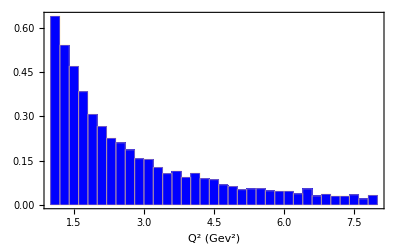

```mathematica
Histogram[Data[[1,All,1]],40,PDF,Frame-> True, FrameLabel->{"Q^2 (Gev^2)"},ChartStyle-> {Blue}]
```

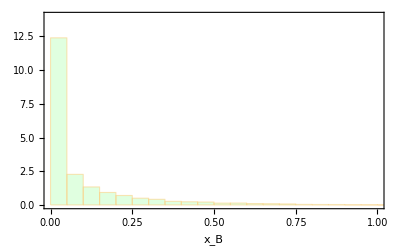

```mathematica
Histogram[Data[[1,All,2]],40,PDF,Frame-> True, FrameLabel->{"x_B"},ChartStyle-> {LightGreen},PlotRange-> {{0,1},{0,14}}]
```

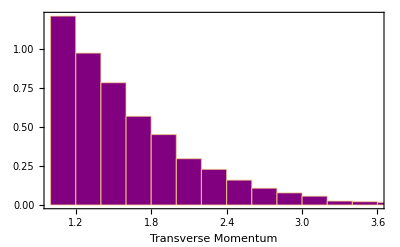

```mathematica
Histogram[Data[[1,All,3]],40,PDF,Frame-> True, FrameLabel->{"Transverse Momentum"},ChartStyle-> {Purple}]
```

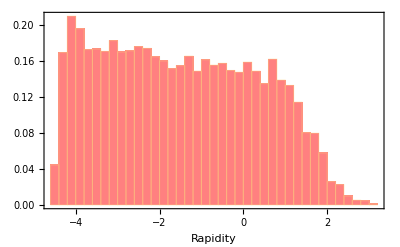

```mathematica
Histogram[Data[[1,All,4]],40,PDF,Frame-> True, FrameLabel->{"Rapidity"},ChartStyle-> {Pink}]
```